Starting configuration for deterministic algorithms:

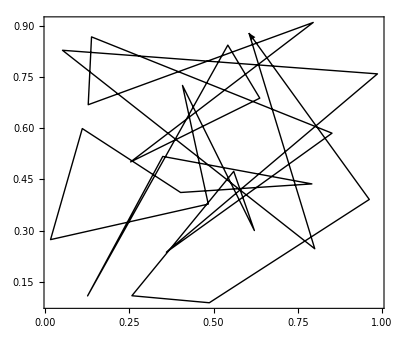

2-Optimal Deterministic Solution: num of steps, distance and tour

17

4.59163

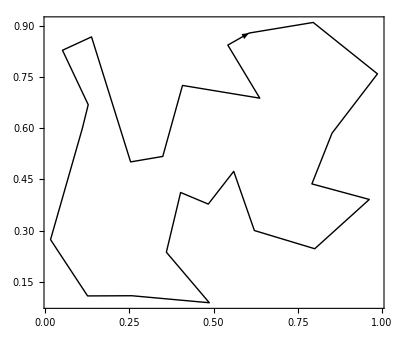

3-Optimal Deterministic Solution: num of steps, distance and tour

18

4.50084

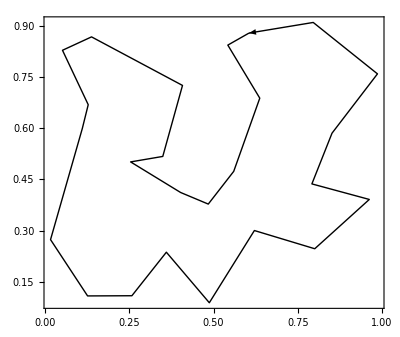

2-Exchange Deterministic Solution: num of steps, distance and tour

14

6.05296

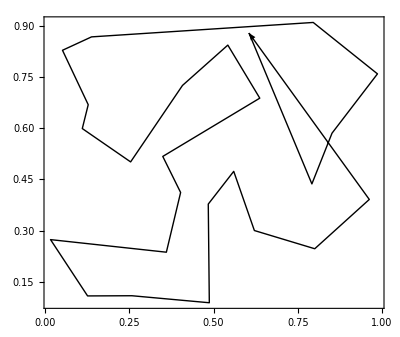

-------------------- SIMULATED ANNEALING (t0=1) --------------------

20379

Simulated Annealing Last Replica Starting Tour

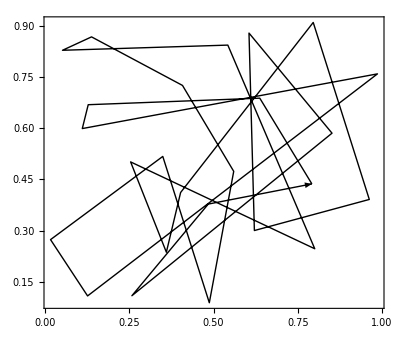

Simulated Annealing Last Replica Solution: num of steps, distance and tour

20379

4.78102

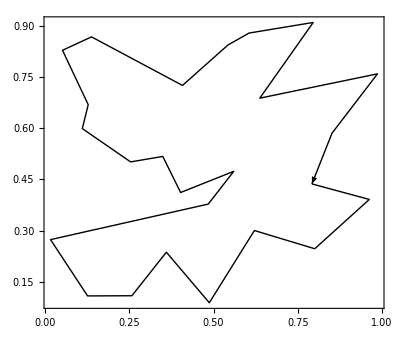

Accepted tour lengths during last replica:

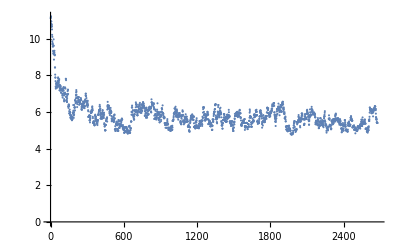

All proposed tour lenghts during last replica:

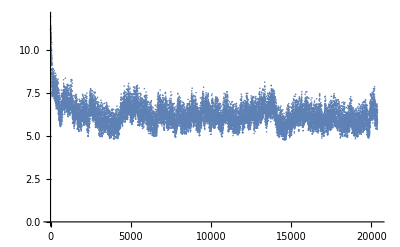

Minimum tour lengths sorted (all replicas):

{4.50084,4.50084,4.51286,4.52033,4.53785,4.56475,4.57067,4.57135,4.57204,4.57453,4.58012,4.58632,4.58721,4.58803,4.58811,4.59265,4.59325,4.59481,4.60082,4.60162,4.6027,4.60383,4.60754,4.61914,4.62199,4.62348,4.62498,4.62834,4.62917,4.63158,4.63412,4.63457,4.64239,4.65659,4.66216,4.66384,4.66732,4.66941,4.68347,4.69677,4.69717,4.703,4.70786,4.71545,4.71824,4.72644,4.73899,4.76343,4.78102,4.81212}

2-optimal tour lengths over all replicas:

{4.50084,4.50084,4.51286,4.52033,4.53785,4.56475,4.57067,4.58012,4.59325,4.60162,4.60383,4.60754,4.62199,4.64239,4.66216,4.66384,4.73899}

2-optimal percentage over all replicas:

34.

2-optimal overlap distribution:

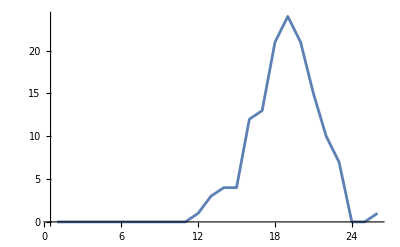

2-optimal triplets overlap distributions:

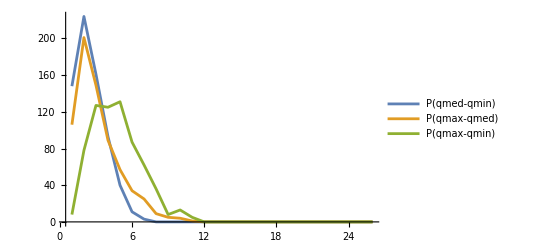

-Graphics3D-

3-optimal tour lengths over all replicas::

{4.50084,4.50084,4.52033,4.57067}

3-optimal percentage over all replicas::

8.

3-optimal overlap distribution:

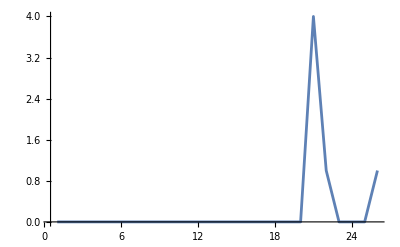

3-optimal triplets overlaps distributions:

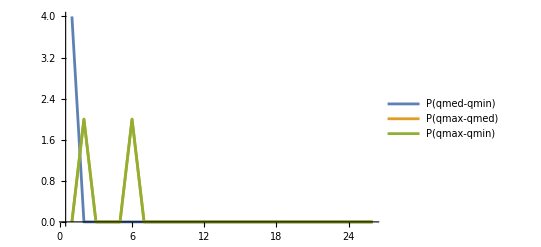

-Graphics3D-

3-optimal percentage over 2-optimal percentage ratio:

0.235294

-------------------- RANDOM PROPOSAL (t0=0) --------------------

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Randoma Proposal Last Replica Starting Tour

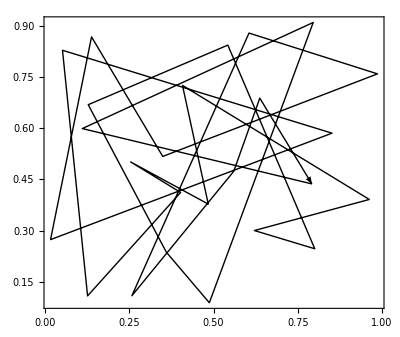

Random Proposal Last Replica Solution: num of steps, distance and tour

1810

4.52033

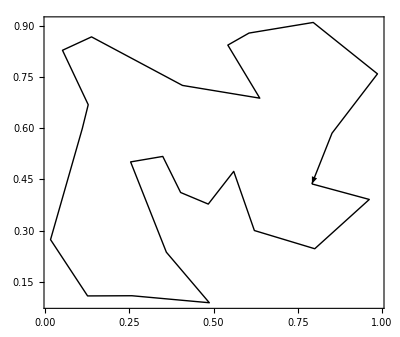

Accepted tour lengths during last replica:

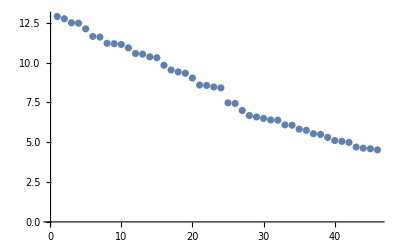

All proposed tour lenghts during last replica:

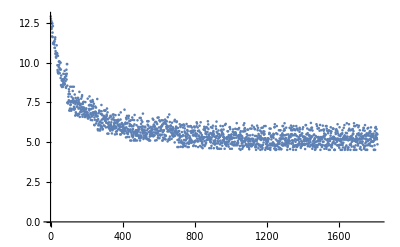

Minimum tour lengths sorted (all replicas):

{4.50084,4.50084,4.52033,4.52033,4.5566,4.59163,4.61957,4.62024,4.6407,4.65182,4.65738,4.66384,4.66738,4.67761,4.67973,4.68113,4.68245,4.69343,4.70104,4.70104,4.71397,4.71734,4.71929,4.72869,4.73265,4.74083,4.74164,4.74536,4.75769,4.78263,4.79217,4.79486,4.80122,4.80762,4.81752,4.82502,4.83439,4.84555,4.85054,4.85299,4.87657,4.89881,4.90604,4.90812,4.9586,4.97329,4.99447,4.99949,5.06261,5.07782}

2-optimal tour lengths over all replicas:

{4.50084,4.50084,4.52033,4.52033,4.59163,4.61957,4.62024,4.6407,4.65182,4.65738,4.66384,4.66738,4.67761,4.68113,4.68245,4.69343,4.70104,4.70104,4.71397,4.71734,4.72869,4.73265,4.74083,4.74164,4.75769,4.78263,4.79217,4.79486,4.80762,4.81752,4.82502,4.83439,4.84555,4.85054,4.85299,4.87657,4.89881,4.90604,4.90812,4.9586,4.97329,4.99447,4.99949,5.06261,5.07782}

2-optimal percentage over all replicas:

90.

2-optimal overlap distribution:

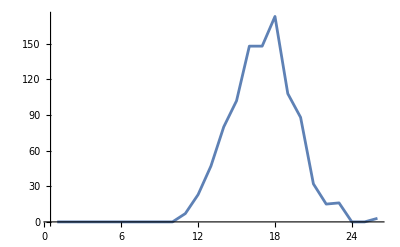

2-optimal triplets overlaps distributions:

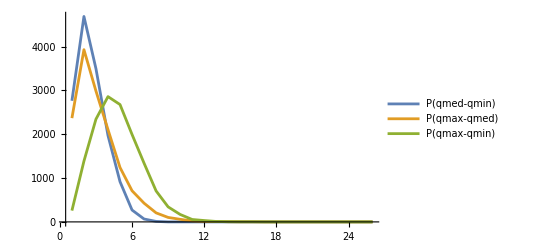

-Graphics3D-

3-optimal tour lengths over all replicas:

{4.50084,4.50084,4.52033,4.52033}

3-optimal percentage over all replicas:

8.

3-optimal overlap distribution:

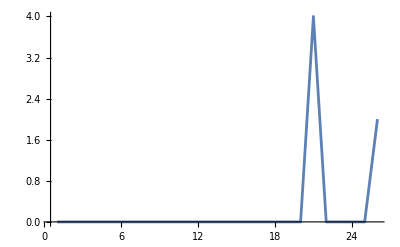

3-optimal triplets overlaps distributions:

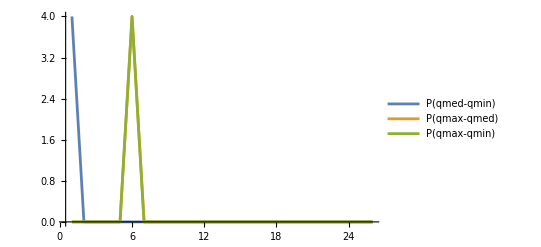

-Graphics3D-

3-optimal percentage over 2-optimal percentage ratio:

0.0888889

```mathematica
(* In this file we propose different algorithms for a solution to the travelling salesman problem. Firstly the 2D cities configuration is generated with customizable cities number and arrangement. Then deterministic algorithms based on specific move strategies are implemented. For every move strategy a different neighbourhood is defined. At each step the new tour is set to the shortest neighbour until some optimality requirements are satisfied. Then a simulated annealing with customizable move strategy, annealing strategy and number of steps is implemented. 2_optimal and 3_optimal solution search functions are implemented and also overlap distributions among the optimal solutions of the same optimality order are studied. A final part is dedicated to the random proposal algorithm, which is nothing but simulated annealing with zero temperature. Also in this case 2_optimal and 3_optimal solutions, with their overlaps, are studied. *)


(* PARAMETERS *)

n=25;    (* number of cities *)
citiesArrangement=1;     (* 1 -> random points; 2 -> regular polygon *)
moveStrategy=2;     (* 1 -> TwoElementsExchange ; 2 -> Lin's 2-link move (TwoMoves) ; 3 -> Lin's 3-link move (ThreeMoves) *) 
nrepl=50;     (* num of replicas with different initial tour *)
annealingStrategy=4;     (* 1 -> t=t0-k*itemp ; 2 -> t=t0/itemp ; 3 -> t=t0^(1/(k*itemp))-1 ; 4 -> t=t0/Log[E+k*itemp] *)
k =1000000*E;     (* linear/exponential/logaritmic temperature vatiation *)
ntemp=10000;     (* num of temperatures steps *)
nsteps=1;     (* num of steps at fixed temperature *)


(* MATRIX OF DISTANCES *)

Switch[citiesArrangement,
1,coords=RandomReal[1,{n,2}] , (*create a set of coordinates for n cities in a 1x1 space centered in (0.5,0.5)*)
2,coords=Table[{Cos[2Pi i/n],Sin[2Pi i /n]},{i,n}]; (* coordinates of a polygonal city configuration *)
];
MatrixForm[coords];
dist=Table[0,{i,n},{j,n}];    (*initialize/clear the distance matrix*)
For[i=1,i<=n,i++,
For[j=1,j<=i,j++, 
dist[[i,j]]=Norm[coords[[i]]-coords[[j]]];
];
];
dist=dist+Transpose[dist]; 
MatrixForm[dist];


(* FUNCTIONS *)

(* function to calculate the total distance of a route adding the distance of each link there present. It is based on the definition of a distance matrix (see below) *)
distcalc[seq_]:=Module[{d=0,i=1},
For[i=1,i<=n,i++,
indeces=seq[[i;;i+1]];
d=d+dist[[indeces[[1]],indeces[[2]]]];
];
d
];

(* function to exchange two randomly sampled cities of the route *)
TwoElementsExchange[seq_]:=Module[{seqnew=Table[0,{i,n+1}]},
seqnew=seq;
indeces=RandomInteger[{2,n},2];
seqnew[[indeces]]=seq[[Reverse[indeces]]];
seqnew
];

(* function to implement the "TwoMoves" move where two random cities of the sequence are exchanged and the sub-sequence contained by them is inverted *)
TwoMoves[seq_]:= Module[{seqnew=Table[0,{i,n+1}]},
seqnew=seq;
indeces=RandomInteger[{2,n},2];
indeces=Sort[indeces];
seqnew[[indeces[[1]];;indeces[[2]]]]=Reverse[seq[[indeces[[1]];;indeces[[2]]]]];
seqnew
];

(* function to implement the "ThreeMoves", for description of this move steps see image in the slides *)
ThreeMoves[seq_]:= Module[{seqnew=Table[0,{i,n+1}]},
seqnew=seq;
indeces=RandomInteger[{1,n},3];
While[indeces[[1]]==indeces[[2]] || indeces[[1]]==indeces[[3]] || indeces[[2]]==indeces[[3]],
indeces=RandomInteger[{1,n},3];
];
indeces=Sort[indeces];
x=RandomReal[];
If[x<0.5,
seqnew[[indeces[[1]]+1;;indeces[[1]]+indeces[[3]]-indeces[[2]]]]=seq[[indeces[[2]]+1;;indeces[[3]]]];
seqnew[[indeces[[1]]+indeces[[3]]-indeces[[2]]+1;;indeces[[3]]]]=seq[[indeces[[1]]+1;;indeces[[2]]]],
seqnew[[indeces[[1]]+1;;indeces[[1]]+indeces[[3]]-indeces[[2]]]]=Reverse[seq[[indeces[[2]]+1;;indeces[[3]]]]];
seqnew[[indeces[[1]]+indeces[[3]]-indeces[[2]]+1;;indeces[[3]]]]=seq[[indeces[[1]]+1;;indeces[[2]]]];
];
seqnew
];

(* function to compute the overlap between two routes; the overlap is defined here as the number of shared links *)
overlap[a_,b_]:=Module[{q=0,i=1,j=1},
For[i=1, i<=n, i++,
For[j=1, j<=n,j++,
If[(a[[i]]==b[[j]]&&a[[i+1]]==b[[j+1]])||(a[[i]]==b[[j+1]]&&a[[i+1]]==b[[j]]),
q++;
];
];
];
q
];


(* STARTING TOUR FOR DETERMINISTIC ALGOTITHMS *)

Print["

Starting configuration for deterministic algorithms:"]
rndmsmpl=RandomSample[Range[n]];
Graphics[Arrow[coords[[Join[rndmsmpl,{rndmsmpl[[1]]}]]]],Frame->True]



(* 2-OPTIMAL DETERMINISTIC ALGORITHM *)

Print["

2-Optimal Deterministic Solution: num of steps, distance and tour"]
seq0=Join[rndmsmpl,{rndmsmpl[[1]]}];   
d0=distcalc[seq0];
seqopt=seq0;
dopt=d0;
For[i=2,i<=n-1,i++,
For[j=i+1,j<=n,j++,
seq1=seq0;
seq1[[i;;j]]=Reverse[seq0[[i;;j]]];
d1=distcalc[seq1];
If[d1<dopt,
seqopt= seq1;
dopt= d1;
];
];
];
count=0;
While[seqopt!=seq0,
seq0=seqopt;
d0=dopt;
For[i=2,i<=n-1,i++,
For[j=i+1,j<=n,j++,
seq1=seq0;
seq1[[i;;j]]=Reverse[seq0[[i;;j]]];
d1=distcalc[seq1];
If[d1<dopt,
seqopt= seq1;
dopt= d1;
];
];
];
count++;
];
count
N[dopt]
Graphics[Arrow[coords[[seqopt]]],Frame->True]



(* 3-OPTIMAL DETERMINISTIC ALGORITHM *)

Print["

3-Optimal Deterministic Solution: num of steps, distance and tour"]
seq0=Join[rndmsmpl,{rndmsmpl[[1]]}];   
d0=distcalc[seq0];
seqopt=seq0;
dopt=d0;
For[i=1,i<=n-2,i++,
For[j=i+1,j<=n-1,j++,
For[k=j+1,k<=n,k++,
seq1=seq0;
seq1[[i+1;;i+k-j]]=seq0[[j+1;;k]];
seq1[[i+k-j+1;;k]]=seq0[[i+1;;j]];
d1=distcalc[seq1];
If[d1<dopt,
seqopt= seq1;
dopt= d1;
];
seq1=seq0;
seq1[[i+1;;i+k-j]]=Reverse[seq0[[j+1;;k]]];
seq1[[i+k-j+1;;k]]=seq0[[i+1;;j]];
d1=distcalc[seq1];
If[d1<dopt,
seqopt= seq1;
dopt= d1;
];
];
];
];
count=0;
While[seqopt!=seq0,
seq0=seqopt;
d0=dopt;
For[i=1,i<=n-2,i++,
For[j=i+1,j<=n-1,j++,
For[k=j+1,k<=n,k++,
seq1=seq0;
seq1[[i+1;;i+k-j]]=seq0[[j+1;;k]];
seq1[[i+k-j+1;;k]]=seq0[[i+1;;j]];
d1=distcalc[seq1];
If[d1<dopt,
seqopt= seq1;
dopt= d1;
];
seq1=seq0;
seq1[[i+1;;i+k-j]]=Reverse[seq0[[j+1;;k]]];
seq1[[i+k-j+1;;k]]=seq0[[i+1;;j]];
d1=distcalc[seq1];
If[d1<dopt,
seqopt= seq1;
dopt= d1;
];
];
];
];
count++;
];
count
N[dopt]
Graphics[Arrow[coords[[seqopt]]],Frame->True]



(* 2-EXCHANGE DETERMINISTIC ALGORITHM *)

Print["

2-Exchange Deterministic Solution: num of steps, distance and tour"]
seq0=Join[rndmsmpl,{rndmsmpl[[1]]}];   
d0=distcalc[seq0];
seqopt=seq0;
dopt=d0;
For[i=2,i<=n-1,i++,
For[j=i+1,j<=n,j++,
seq1=seq0;
temp=seq1[[i]];
seq1[[i]]=seq1[[j]];
seq1[[j]]=temp;
d1=distcalc[seq1];
If[d1<dopt,
seqopt= seq1;
dopt= d1;
];
];
];
count=0;
While[seqopt!=seq0 ,
seq0=seqopt;
d0=dopt;
For[i=3,i<=n-1,i++,
For[j=2,j<i,j++,
seq1=seq0;
temp=seq1[[i]];
seq1[[i]]=seq1[[j]];
seq1[[j]]=temp;
d1=distcalc[seq1];
If[d1<dopt,
seqopt= seq1;
dopt= d1;
];
];
];
count++;
];
count
N[dopt]
Graphics[Arrow[coords[[seqopt]]],Frame->True]



Print["

-------------------- SIMULATED ANNEALING (t0=1) --------------------

"]



(* SIMULATED ANNEALING ALGORITHM *)
ntemp=Ceiling[20378.390175293116]
t0=1;
SEQMIN=Table[0,{i,nrepl},{j,n+1}];
DMIN=Table[0,{i,nrepl}];
For[irepl=1,irepl<=nrepl,irepl++,
itemp=0;
istep=0;
rndmsmpl=RandomSample[Range[n]];
seq0=Join[rndmsmpl,{rndmsmpl[[1]]}]; (*the length of the sequence is n+1 (closed loop)*)
d0=distcalc[seq0];
seqmin=seq0;
dmin=d0;
Dacp={N[d0]};
Dall={N[d0]};
(*Print["irepl, itemp, isteps, seqmin, dmin, t"];
Print[{irepl,itemp,isteps,seqmin,NumberForm[N[dmin],4],t0}];*)

For[itemp=0,itemp<=ntemp,itemp++,
Switch[annealingStrategy,
1,t=t0-k*itemp,
2,t=t0/itemp,
3,t=t0^(1/(k*itemp)),
4,t=t0/Log[E+k*itemp];
];

For [isteps=1,isteps<=nsteps,isteps++,
Switch[moveStrategy,
1,seq1=TwoElementsExchange[seq0],
2,seq1=TwoMoves[seq0],
3,seq1=ThreeMoves[seq0];
];
d1=distcalc[seq1];
Dall=Join[Dall,{N[d1]}];
If[d1<d0,
seq0=seq1;
d0=d1;
Dacp=Join[Dacp,{N[d0]}];
If[d0<dmin,
seqmin=seq0;
dmin=d0;
(*Print[{irepl,itemp,isteps,seqmin,NumberForm[N[dmin],4],NumberForm[N[t],4]}];*)
],
prob=Exp[-(d1-d0)/t];
r=RandomReal[];
If[r<prob,
seq0=seq1;
d0=d1;
Dacp=Join[Dacp,{N[d0]}];
];
];
];
];
(*Print["
-------------- Replica --------------
"];*)
SEQMIN[[irepl]]=seqmin;
DMIN[[irepl]]=dmin;
];
Print["

Simulated Annealing Last Replica Starting Tour"]
Graphics[Arrow[coords[[Join[rndmsmpl,{rndmsmpl[[1]]}]]]],Frame->True]

Print["

Simulated Annealing Last Replica Solution: num of steps, distance and tour"]
nsteps*ntemp
Last[DMIN]
Graphics[Arrow[coords[[seqmin]]],Frame->True]
Print["Accepted tour lengths during last replica:"]
ListPlot[Dacp,PlotRange->All]
Print["All proposed tour lenghts during last replica:"]
ListPlot[Dall,PlotRange->All]
Print["Minimum tour lengths sorted (all replicas):"]
Sort[DMIN]



(* 2_OPTIMAL SIMULATED ANNEALING SOLUTIONS SEARCH: this block is meant to calculate how many of the solutions in DMIN are 2-optimal. 2-optimality means that the solution is a minimum for any change of any 2 links in the sequence *)
iopt=0;
SEQOPT2={};
DOPT2={};
For[irepl=1,irepl<=nrepl,irepl++,
check=1;
For[i=2,i<=n-1,i++,
For[j=i+1,j<=n,j++,
neighbor=SEQMIN[[irepl]];
neighbor[[i;;j]]=Reverse[SEQMIN[[irepl]][[i;;j]]];
If[distcalc[neighbor]<DMIN[[irepl]],
check=0;
];
];
];
If[check==1,
SEQOPT2=Join[SEQOPT2,{SEQMIN[[irepl]]}];
DOPT2=Join[DOPT2,{DMIN[[irepl]]}];
iopt++;
];
];
Print["2-optimal tour lengths over all replicas:"]
Sort[DOPT2]
Print["2-optimal percentage over all replicas:"]
TwoOptPerc=N[(iopt*100)/nrepl]



(* 2-OPTIMAL SOLUTION OVERLAP DISTRIBUTIONS *)

Pq=Table[0,{i,n+1}];   (*initializing the overlap distribution*)
For[l=1,l<=iopt-1, l++,
For[m=l+1,m<=iopt,m++,
q=overlap[SEQOPT2[[l]],SEQOPT2[[m]]];
Pq[[q+1]]=Pq[[q+1]]+1;   (*Wolfram conta gli elementi di un vettore a partire da 1...*)
];
];
Print["2-optimal overlap distribution:"]
ListLinePlot[Pq,PlotRange->All]

Px=Table[0,{i,n+1}]; 
Py=Table[0,{i,n+1}]; 
Pz=Table[0,{i,n+1}]; 
PQminmed=Table[0,{i,n+1},{j,n+1}];
For[r=1,r<=iopt-2,r++,
For[s=r+1,s<=iopt-1,s++,
For[t=s+1,t<=iopt,t++,
q12=overlap[SEQOPT2[[r]],SEQOPT2[[s]]];
q13=overlap[SEQOPT2[[r]],SEQOPT2[[t]]];
q23=overlap[SEQOPT2[[s]],SEQOPT2[[t]]];
qtrip=Sort[{q12,q13,q23}];
x=qtrip[[2]]-qtrip[[1]];  (*this should be 0 if the space is ultrametric*)
y=qtrip[[3]]-qtrip[[2]];
z=qtrip[[3]]-qtrip[[1]];  (*y and z should be equal if the space is ultrametric*)
Px[[x+1]]=Px[[x+1]]+1;
Py[[y+1]]=Py[[y+1]]+1;
Pz[[z+1]]=Pz[[z+1]]+1;
PQminmed[[qtrip[[1]]+1]][[qtrip[[2]]+1]]=PQminmed[[qtrip[[1]]+1]][[qtrip[[2]]+1]]+1;
];
];
];
Print["2-optimal triplets overlap distributions:"]
ListLinePlot[{Px,Py,Pz},PlotLegends->{"P(qmed-qmin)","P(qmax-qmed)","P(qmax-qmin)"},PlotRange->All]
ListPlot3D[PQminmed]



(* 3_OPTIMAL SIMULATED ANNEALING SOLUTIONS SEARCH: this block is meant to calculate how many of the solutions in DMIN are 3-optimal. 3-optimality means that the solution is a minimum for any change of any 3 links in the sequence *)

iopt=0;
SEQOPT3={};
DOPT3={};
For[iopt2=1,iopt2<=Length[SEQOPT2],iopt2++, (* we look for 3-opt in the subset of 2-opt because we know that the set of (n+1)-opt is contained in the set of n-opt *)
check=1;
For[i=1,i<=n-2,i++,
For[j=i+1,j<=n-1,j++,
For[k=j+1,k<=n,k++,
neighbor=SEQOPT2[[iopt2]];
neighbor[[i+1;;i+k-j]]=SEQOPT2[[iopt2]][[j+1;;k]];
neighbor[[i+k-j+1;;k]]=SEQOPT2[[iopt2]][[i+1;;j]];
If[distcalc[neighbor]<DOPT2[[iopt2]],
check=0;
];
neighbor=SEQOPT2[[iopt2]];
neighbor[[i+1;;i+k-j]]=Reverse[SEQOPT2[[iopt2]][[j+1;;k]]];
neighbor[[i+k-j+1;;k]]=SEQOPT2[[iopt2]][[i+1;;j]];
If[distcalc[neighbor]<DOPT2[[iopt2]],
check=0;
];
];
];
];
If[check==1,
SEQOPT3=Join[SEQOPT3,{SEQOPT2[[iopt2]]}];
DOPT3=Join[DOPT3,{DOPT2[[iopt2]]}];
iopt++;
];
];
Print["3-optimal tour lengths over all replicas::"]
Sort[DOPT3]
Print["3-optimal percentage over all replicas::"]
ThreeOptPerc=N[(iopt*100)/nrepl]



(* 3-OPTIMAL SOLUTION OVERLAP DISTRIBUTIONS *)

Pq=Table[0,{i,n+1}];   (*initializing the overlap distribution*)
For[l=1,l<=iopt-1, l++,
For[m=l+1,m<=iopt,m++,
q=overlap[SEQOPT3[[l]],SEQOPT3[[m]]];
Pq[[q+1]]=Pq[[q+1]]+1;   (*Wolfram conta gli elementi di un vettore a partire da 1...*)
];
];
Print["3-optimal overlap distribution:"]
ListLinePlot[Pq,PlotRange->All]

Px=Table[0,{i,n+1}]; 
Py=Table[0,{i,n+1}]; 
Pz=Table[0,{i,n+1}]; 
PQminmed=Table[0,{i,n+1},{j,n+1}];
For[r=1,r<=iopt-2,r++,
For[s=r+1,s<=iopt-1,s++,
For[t=s+1,t<=iopt,t++,
q12=overlap[SEQOPT3[[r]],SEQOPT3[[s]]];
q13=overlap[SEQOPT3[[r]],SEQOPT3[[t]]];
q23=overlap[SEQOPT3[[s]],SEQOPT3[[t]]];
qtrip=Sort[{q12,q13,q23}];
x=qtrip[[2]]-qtrip[[1]];  (*this should be a 0 if the space is ultrametric*)
y=qtrip[[3]]-qtrip[[2]];
z=qtrip[[3]]-qtrip[[1]];  (*y and z should be equal if the space is ultrametric*)
Px[[x+1]]=Px[[x+1]]+1;
Py[[y+1]]=Py[[y+1]]+1;
Pz[[z+1]]=Pz[[z+1]]+1;
PQminmed[[qtrip[[1]]+1]][[qtrip[[2]]+1]]=PQminmed[[qtrip[[1]]+1]][[qtrip[[2]]+1]]+1;
];
];
];
Print["3-optimal triplets overlaps distributions:"]
ListLinePlot[{Px,Py,Pz},PlotLegends->{"P(qmed-qmin)","P(qmax-qmed)","P(qmax-qmin)"},PlotRange->All]
ListPlot3D[PQminmed]

Print["3-optimal percentage over 2-optimal percentage ratio:"]
ThreeOptPerc/TwoOptPerc



Print["


-------------------- RANDOM PROPOSAL (t0=0) --------------------
"]



(* RANDOM PROPOSAL ALGORITHM: ANNEALING WITH t0=0 *)
ntemp=Ceiling[1809.8721913024297];
t0=0;
SEQMIN=Table[0,{i,nrepl},{j,n+1}];
DMIN=Table[0,{i,nrepl}];
For[irepl=1,irepl<=nrepl,irepl++,
itemp=0;
istep=0;
rndmsmpl=RandomSample[Range[n]];
seq0=Join[rndmsmpl,{rndmsmpl[[1]]}]; (*the length of the sequence is n+1 (closed loop)*)
d0=distcalc[seq0];
seqmin=seq0;
dmin=d0;
Dacp={N[d0]};
Dall={N[d0]};
(*Print["irepl, itemp, isteps, seqmin, dmin, t"];
Print[{irepl,itemp,isteps,seqmin,NumberForm[N[dmin],4],t0}];*)

For[itemp=0,itemp<=ntemp,itemp++,
Switch[annealingStrategy,
1,t=t0-k*itemp,
2,t=t0/itemp,
3,t=t0^(1/(k*itemp)),
4,t=t0/Log[E+k*itemp];
];

For [isteps=1,isteps<=nsteps,isteps++,
Switch[moveStrategy,
1,seq1=TwoElementsExchange[seq0],
2,seq1=TwoMoves[seq0],
3,seq1=ThreeMoves[seq0];
];
d1=distcalc[seq1];
Dall=Join[Dall,{N[d1]}];
If[d1<d0,
seq0=seq1;
d0=d1;
Dacp=Join[Dacp,{N[d0]}];
If[d0<dmin,
seqmin=seq0;
dmin=d0;
(*Print[{irepl,itemp,isteps,seqmin,NumberForm[N[dmin],4],NumberForm[N[t],4]}];*)
],
prob=Exp[-(d1-d0)/t];
r=RandomReal[];
If[r<prob,
seq0=seq1;
d0=d1;
Dacp=Join[Dacp,{N[d0]}];
];
];
];
];
(*Print["
-------------- Replica --------------
"];*)
SEQMIN[[irepl]]=seqmin;
DMIN[[irepl]]=dmin;
];
Print["

Randoma Proposal Last Replica Starting Tour"]
Graphics[Arrow[coords[[Join[rndmsmpl,{rndmsmpl[[1]]}]]]],Frame->True]
Print["Random Proposal Last Replica Solution: num of steps, distance and tour"]
nsteps*ntemp
Last[DMIN]
Graphics[Arrow[coords[[seqmin]]],Frame->True]
Print["Accepted tour lengths during last replica:"]
ListPlot[Dacp,PlotRange->All]
Print["All proposed tour lenghts during last replica:"]
ListPlot[Dall,PlotRange->All]
Print["Minimum tour lengths sorted (all replicas):"]
Sort[DMIN]



(* 2-OPTIMAL RANDOM PROPOSAL SOLUTIONS SEARCH *)

iopt=0;
SEQOPT2={};
DOPT2={};
For[irepl=1,irepl<=nrepl,irepl++,
check=1;
For[i=2,i<=n-1,i++,
For[j=i+1,j<=n,j++,
neighbor=SEQMIN[[irepl]];
neighbor[[i;;j]]=Reverse[SEQMIN[[irepl]][[i;;j]]];
If[distcalc[neighbor]<DMIN[[irepl]],
check=0;
];
];
];
If[check==1,
SEQOPT2=Join[SEQOPT2,{SEQMIN[[irepl]]}];
DOPT2=Join[DOPT2,{DMIN[[irepl]]}];
iopt++;
];
];
Print["2-optimal tour lengths over all replicas:"]
Sort[DOPT2]
Print["2-optimal percentage over all replicas:"]
TwoOptPerc=N[(iopt*100)/nrepl]



(* 2-OPTIMAL RANDOM PROPOSAL SOLUTION OVERLAP DISTRIBUTIONS *)

Pq=Table[0,{i,n+1}];   (*initializing the overlap distribution*)
For[l=1,l<=iopt-1, l++,
For[m=l+1,m<=iopt,m++,
q=overlap[SEQOPT2[[l]],SEQOPT2[[m]]];
Pq[[q+1]]=Pq[[q+1]]+1;   (*Wolfram conta gli elementi di un vettore a partire da 1...*)
];
];
Print["2-optimal overlap distribution:"]
ListLinePlot[Pq,PlotRange->All]

Px=Table[0,{i,n+1}]; 
Py=Table[0,{i,n+1}]; 
Pz=Table[0,{i,n+1}]; 
PQminmed=Table[0,{i,n+1},{j,n+1}];
For[r=1,r<=iopt-2,r++,
For[s=r+1,s<=iopt-1,s++,
For[t=s+1,t<=iopt,t++,
q12=overlap[SEQOPT2[[r]],SEQOPT2[[s]]];
q13=overlap[SEQOPT2[[r]],SEQOPT2[[t]]];
q23=overlap[SEQOPT2[[s]],SEQOPT2[[t]]];
qtrip=Sort[{q12,q13,q23}];
x=qtrip[[2]]-qtrip[[1]];  (*this should be a 0 if the space is ultrametric*)
y=qtrip[[3]]-qtrip[[2]];
z=qtrip[[3]]-qtrip[[1]];  (*y and z should be equal if the space is ultrametric*)
Px[[x+1]]=Px[[x+1]]+1;
Py[[y+1]]=Py[[y+1]]+1;
Pz[[z+1]]=Pz[[z+1]]+1;
PQminmed[[qtrip[[1]]+1]][[qtrip[[2]]+1]]=PQminmed[[qtrip[[1]]+1]][[qtrip[[2]]+1]]+1;
];
];
];
Print["2-optimal triplets overlaps distributions:"]
ListLinePlot[{Px,Py,Pz},PlotLegends->{"P(qmed-qmin)","P(qmax-qmed)","P(qmax-qmin)"},PlotRange->All]
ListPlot3D[PQminmed]



(* 3-OPTIMAL RANDOM PROPOSAL SOLUTIONS SEARCH *)

iopt=0;
SEQOPT3={};
DOPT3={};
For[iopt2=1,iopt2<=Length[SEQOPT2],iopt2++, (* we look for 3-opt in the subset of 2-opt because we know that the set of (n+1)-opt is contained in the set of n-opt *)
check=1;
For[i=1,i<=n-2,i++,
For[j=i+1,j<=n-1,j++,
For[k=j+1,k<=n,k++,
neighbor=SEQOPT2[[iopt2]];
neighbor[[i+1;;i+k-j]]=SEQOPT2[[iopt2]][[j+1;;k]];
neighbor[[i+k-j+1;;k]]=SEQOPT2[[iopt2]][[i+1;;j]];
If[distcalc[neighbor]<DOPT2[[iopt2]],
check=0;
];
neighbor=SEQOPT2[[iopt2]];
neighbor[[i+1;;i+k-j]]=Reverse[SEQOPT2[[iopt2]][[j+1;;k]]];
neighbor[[i+k-j+1;;k]]=SEQOPT2[[iopt2]][[i+1;;j]];
If[distcalc[neighbor]<DOPT2[[iopt2]],
check=0;
];
];
];
];
If[check==1,
SEQOPT3=Join[SEQOPT3,{SEQOPT2[[iopt2]]}];
DOPT3=Join[DOPT3,{DOPT2[[iopt2]]}];
iopt++;
];
];
Print["3-optimal tour lengths over all replicas:"]
Sort[DOPT3]
Print["3-optimal percentage over all replicas:"]
ThreeOptPerc=N[(iopt*100)/nrepl]

Pq=Table[0,{i,n+1}];   (*initializing the overlap distribution*)
For[l=1,l<=iopt-1, l++,
For[m=l+1,m<=iopt,m++,
q=overlap[SEQOPT3[[l]],SEQOPT3[[m]]];
Pq[[q+1]]=Pq[[q+1]]+1;   (*Wolfram conta gli elementi di un vettore a partire da 1...*)
];
];
Print["3-optimal overlap distribution:"]
ListLinePlot[Pq,PlotRange->All]

Px=Table[0,{i,n+1}]; 
Py=Table[0,{i,n+1}]; 
Pz=Table[0,{i,n+1}]; 
PQminmed=Table[0,{i,n+1},{j,n+1}];
For[r=1,r<=iopt-2,r++,
For[s=r+1,s<=iopt-1,s++,
For[t=s+1,t<=iopt,t++,
q12=overlap[SEQOPT3[[r]],SEQOPT3[[s]]];
q13=overlap[SEQOPT3[[r]],SEQOPT3[[t]]];
q23=overlap[SEQOPT3[[s]],SEQOPT3[[t]]];
qtrip=Sort[{q12,q13,q23}];
x=qtrip[[2]]-qtrip[[1]];  (*this should be a 0 if the space is ultrametric*)
y=qtrip[[3]]-qtrip[[2]];
z=qtrip[[3]]-qtrip[[1]];  (*y and z should be equal if the space is ultrametric*)
Px[[x+1]]=Px[[x+1]]+1;
Py[[y+1]]=Py[[y+1]]+1;
Pz[[z+1]]=Pz[[z+1]]+1;
PQminmed[[qtrip[[1]]+1]][[qtrip[[2]]+1]]=PQminmed[[qtrip[[1]]+1]][[qtrip[[2]]+1]]+1;
];
];
];
Print["3-optimal triplets overlaps distributions:"]
ListLinePlot[{Px,Py,Pz},PlotLegends->{"P(qmed-qmin)","P(qmax-qmed)","P(qmax-qmin)"},PlotRange->All]
ListPlot3D[PQminmed]

Print["3-optimal percentage over 2-optimal percentage ratio:"]
ThreeOptPerc/TwoOptPerc
```